Caustics Simulator Starting...

Creating surface (lambda=0.45m)...

Rendering test frame...

Displaying...

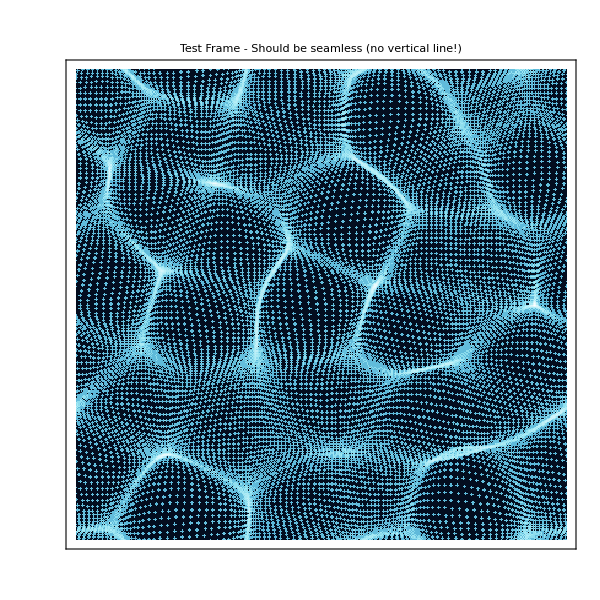

*** Generating animation (60 frames)... ***

Frame 0/60

Frame 10/60

Frame 20/60

Frame 30/60

Frame 40/60

Frame 50/60

Creating animation...

```mathematica
(* WORKING CAUSTICS - Fixed boundary artifacts *)

Print["Caustics Simulator Starting..."];

(* ========================================================================= *)
(* Helpers *)
(* ========================================================================= *)

sunDirection[elevDeg_, azDeg_] := Module[{elev, az, sx, sy, sz},
  elev = elevDeg * Degree;
  az = azDeg * Degree;
  sx = Cos[elev] * Cos[az];
  sy = Cos[elev] * Sin[az];
  sz = -Sin[elev];
  Normalize[{sx, sy, sz}]
];

(* FIXED: Compute gradient with proper periodic boundaries *)
gradient2D[h_, dx_, dy_] := Module[{ny, nx, hPadX, hPadY, gradX, gradY},
  {ny, nx} = Dimensions[h];

  (* Proper periodic padding using ArrayPad *)
  hPadX = ArrayPad[h, {{0, 0}, {1, 1}}, "Periodic"];  (* Pad columns *)
  hPadY = ArrayPad[h, {{1, 1}, {0, 0}}, "Periodic"];  (* Pad rows *)

  (* Central differences *)
  gradX = Table[
    (hPadX[[j, i+1]] - hPadX[[j, i-1]])/(2*dx),
    {j, ny}, {i, 2, nx+1}
  ];
  gradY = Table[
    (hPadY[[j+1, i]] - hPadY[[j-1, i]])/(2*dy),
    {j, 2, ny+1}, {i, nx}
  ];

  {gradX, gradY}
];

(* ========================================================================= *)
(* Surface *)
(* ========================================================================= *)

createSurface[Nx_, Ny_, Lx_, Ly_, depth_, rms_, lambda0_, seed_] := Module[
  {dx, dy, g, kx, ky, KX, KY, k, omega, k0, sigma, S, h0, h0conj, scale, h0test, x, y, X, Y},

  dx = Lx/Nx; dy = Ly/Ny; g = 9.81;
  SeedRandom[seed];

  (* Frequency grid *)
  kx = 2*Pi*Join[Range[0, Floor[Nx/2]-1], Range[-Ceiling[Nx/2], -1]]/Lx;
  ky = 2*Pi*Join[Range[0, Floor[Ny/2]-1], Range[-Ceiling[Ny/2], -1]]/Ly;
  KX = ConstantArray[kx, Ny];
  KY = Transpose[ConstantArray[ky, Nx]];
  k = Sqrt[KX^2 + KY^2];

  (* Dispersion *)
  omega = Sqrt[g * k * Tanh[k * depth]];
  omega = omega /. {Indeterminate -> 0, ComplexInfinity -> 0};

  (* Spectrum *)
  k0 = 2*Pi/lambda0;
  sigma = 0.16 * k0;
  S = Exp[-0.5*((k - k0)/sigma)^2] * Exp[-(k/(3*k0))^4];
  S = S /. {Indeterminate -> 0};

  (* Random amplitudes *)
  h0 = (RandomVariate[NormalDistribution[], {Ny, Nx}] +
        I*RandomVariate[NormalDistribution[], {Ny, Nx}]) * Sqrt[S/2];

  (* Hermitian symmetry *)
  h0conj = Conjugate[h0[[
    Table[Mod[-i, Ny]+1, {i, 0, Ny-1}],
    Table[Mod[-i, Nx]+1, {i, 0, Nx-1}]
  ]]];

  (* Scale to RMS *)
  h0test = Re[InverseFourier[h0 + h0conj, FourierParameters -> {1, -1}]];
  scale = rms / StandardDeviation[Flatten[h0test]];
  h0 = h0 * scale;
  h0conj = h0conj * scale;

  (* Spatial grid *)
  x = Range[0, Lx-dx, dx];
  y = Range[0, Ly-dy, dy];
  X = ConstantArray[x, Ny];
  Y = Transpose[ConstantArray[y, Nx]];

  <|"omega" -> omega, "h0" -> h0, "h0conj" -> h0conj, "X" -> X, "Y" -> Y,
    "Lx" -> Lx, "Ly" -> Ly, "dx" -> dx, "dy" -> dy, "depth" -> depth|>
];

getHeight[surf_, t_] := Re[InverseFourier[
  surf["h0"] * Exp[I*surf["omega"]*t] + surf["h0conj"] * Exp[-I*surf["omega"]*t],
  FourierParameters -> {1, -1}
]];

(* ========================================================================= *)
(* Rendering *)
(* ========================================================================= *)

renderFrame[surf_, t_, res_] := Module[
  {h, X, Y, dx, dy, Lx, Ly, depth, gradX, gradY, denom, nx, ny, nz,
   sunDir, sx, sy, sz, cosi, eta, k, sqrtk, c2, tx, ty, tz,
   s, bx, by, r0, R, T, w, good, xv, yv, wv, ix, iy, img, mean, maxval},

  (* Surface *)
  h = getHeight[surf, t];
  X = surf["X"]; Y = surf["Y"];
  dx = surf["dx"]; dy = surf["dy"];
  Lx = surf["Lx"]; Ly = surf["Ly"];
  depth = surf["depth"];

  (* Gradients *)
  {gradX, gradY} = gradient2D[h, dx, dy];

  (* Normals *)
  denom = Sqrt[1 + gradX^2 + gradY^2];
  nx = -gradX/denom;
  ny = -gradY/denom;
  nz = 1/denom;

  (* Refraction *)
  sunDir = sunDirection[62, 25];
  {sx, sy, sz} = sunDir;
  cosi = Clip[-(nx*sx + ny*sy + nz*sz), {0, 1}];
  eta = 1/1.333;
  k = 1 - eta^2*(1 - cosi^2);
  sqrtk = Sqrt[Clip[k, {0, Infinity}]];
  c2 = eta*cosi - sqrtk;
  tx = eta*sx + c2*nx;
  ty = eta*sy + c2*ny;
  tz = eta*sz + c2*nz;

  (* Intersect bottom *)
  s = (-depth - h)/(tz - 1*^-20);
  bx = Mod[X + s*tx, Lx];
  by = Mod[Y + s*ty, Ly];

  (* Weights *)
  r0 = ((1 - 1.333)/(1 + 1.333))^2;
  R = r0 + (1 - r0)*(1 - cosi)^5;
  T = 1 - R;
  w = T * cosi / Clip[nz, {1*^-8, Infinity}];

  (* Filter valid rays (downward) *)
  good = Flatten[Position[Flatten[tz], _?((# < 0)&)]];
  xv = Flatten[bx][[good]];
  yv = Flatten[by][[good]];
  wv = Flatten[w][[good]];

  (* Accumulate *)
  img = ConstantArray[0.0, {res, res}];
  ix = Clip[Floor[(xv/Lx)*res] + 1, {1, res}];
  iy = Clip[Floor[(yv/Ly)*res] + 1, {1, res}];
  Do[img[[iy[[i]], ix[[i]]]] += wv[[i]], {i, Length[wv]}];

  (* Simple blur *)
  img = (img +
         RotateRight[img, {0, 1}] + RotateLeft[img, {0, 1}] +
         RotateRight[img, {1, 0}] + RotateLeft[img, {1, 0}])/5.0;

  (* Tonemap *)
  mean = Mean[Flatten[img]];
  img = img / (mean + 1*^-12);
  img = Log[1 + 70*img];
  maxval = Max[Flatten[img]];
  img = img / (maxval + 1*^-12);
  img^0.8
];

(* ========================================================================= *)
(* Water colors *)
(* ========================================================================= *)

waterColor = Blend[{
  {0, RGBColor[0.01, 0.05, 0.12]},
  {0.25, RGBColor[0.02, 0.2, 0.4]},
  {0.5, RGBColor[0, 0.45, 0.7]},
  {0.75, RGBColor[0.6, 0.9, 0.95]},
  {1, RGBColor[1, 1, 1]}
}, #]&;

(* ========================================================================= *)
(* Main *)
(* ========================================================================= *)

Print["Creating surface (lambda=0.45m)..."];
surface = createSurface[128, 128, 2.0, 2.0, 1.2, 0.008, 0.45, 3];

Print["Rendering test frame..."];
test = renderFrame[surface, 0.5, 400];

Print["Displaying..."];
ArrayPlot[test, ColorFunction -> waterColor, ColorFunctionScaling -> False,
  PlotLabel -> "Test Frame - Should be seamless (no vertical line!)",
  ImageSize -> 600, Frame -> True]

(* Generate animation *)
Print["\n*** Generating animation (60 frames)... ***"];
frames = Table[
  If[Mod[k, 10] == 0, Print["Frame ", k, "/60"]];
  renderFrame[surface, k/30.0, 400],
  {k, 0, 59}
];

Print["Creating animation..."];
ListAnimate[
  Table[
    ArrayPlot[frames[[k]],
      ColorFunction -> waterColor,
      ColorFunctionScaling -> False,
      PlotLabel -> Row[{"Pool Caustics  |  t = ", NumberForm[k/30.0, {4, 2}], " s"}],
      ImageSize -> 600,
      Frame -> True
    ],
    {k, 1, 60}
  ],
  AnimationRunning -> True
]
```